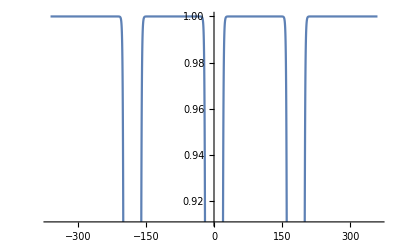

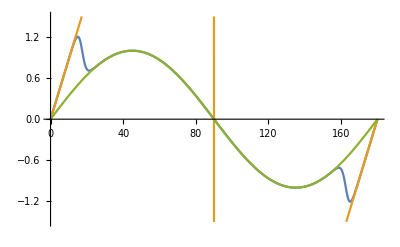

```mathematica
CLa=5;
M=50;
CLa0=0.30;
sigma[a_,a0_]=(1+Exp[-M*(a-a0)]+Exp[M*(a+a0)])/((1+Exp[-M*(a-a0)])*(1+Exp[M*(a+a0)]));
s[a_]=sigma[a,CLa0]*sigma[Pi-a,CLa0]*sigma[Pi+a,CLa0];
Plot[s[a/180*Pi],{a,-360,360}]
CL1[a_]:=CLa*a/;-Pi/2<a<Pi/2;
CL1[a_]:=CLa*(a-Pi)/;Pi/2<=a<3Pi/2;
CL1[a_]:=CLa*(a-Pi)/;a≥3Pi/2;
CL1[a_]:=CLa*(a+Pi)/;-3Pi/2≤a≤-Pi/2;
CL1[a_]:=CLa*(a+Pi)/;a≤-3Pi/2;
CL2[a_]=Sin[2a];
CL[a_]=(1-s[a])CL1[a]+s[a]CL2[a];
Plot[{CL[a/180*Pi],CL1[a/180*Pi],CL2[a/180*Pi]},{a,0,180},PlotRange->1.5]
```

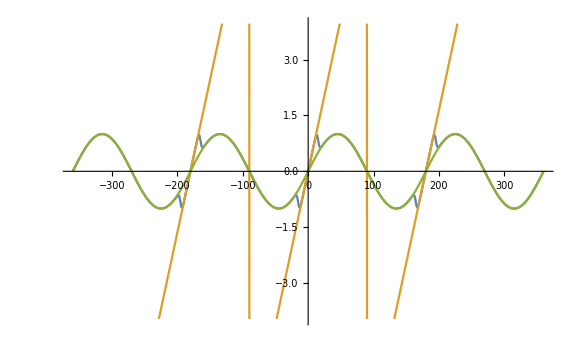

```mathematica
Show[%320,ImageSize->Large]
```

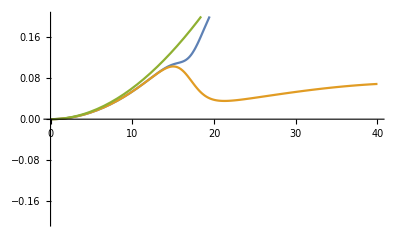

```mathematica
e=0.9;
AR=5;
CD0[a_]=CL[a]*CL[a]/(Pi*e*AR);
CD1[a_]:=CD0[a]/;-Pi/2<a<Pi/2;
CD1[a_]:=CD0[a-Pi]/;Pi/2<=a<3Pi/2;
CD1[a_]:=CD0[a-Pi]/;a≥3Pi/2;
CD1[a_]:=CD0[a+Pi]/;-3Pi/2≤a≤-Pi/2;
CD1[a_]:=CD0[a+Pi]/;a≤-3Pi/2;
CD2[a_]=2Sin[a]^2;
CD[a_]=(1-s[a])CD1[a]+s[a]CD2[a];
Plot[{CD[a/180*Pi],CD1[a/180*Pi],CD2[a/180*Pi]},{a,0,40},PlotRange->0.2]
```

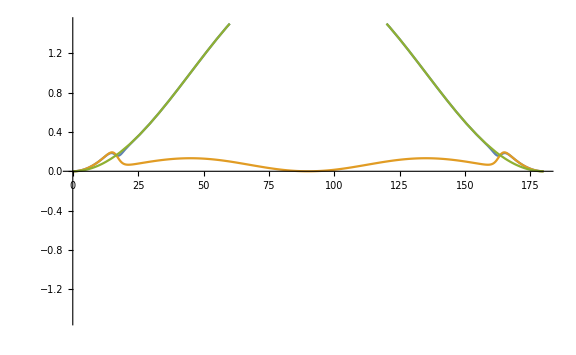

```mathematica
Show[%530,ImageSize->Large]
```

```mathematica
a0
```

0.4712

```mathematica
Delete[a0]
```

Delete[0.4712]

```mathematica
a0
```

0.4712

```mathematica
Clear[a0]
```

```mathematica
CL1[a]
```

3.45 (a+π)

```mathematica
CL1[a]
```

3.45 (a+π)

```mathematica
Clear[CL1]
```

```mathematica
Plot[
```

```mathematica
CL1[Pi/6]
```

2.46091

```mathematica
CL[Pi/12+0.01]
```

1.26252

```mathematica
FindMaximum[CL[x],{x,0}]
```

{1.,{x→0.785398}}

```mathematica
Maximize[CL[x],x ]
```

{1.,{x→0.785398}}